Sistema de ecuaciones original:

```mathematica
TraditionalForm[x[k+1]==A*x[k]*Exp[-α*x[k]-γ*y[k]]]
```

x(k+1)==A x(k) ⅇ^(-α x(k)-γ y(k))

```mathematica
TraditionalForm[y[k+1]==A*b*γ*x[k]*y[k]*Exp[-α*x[k]-γ*y[k]]]
```

y(k+1)==A b γ x(k) y(k) ⅇ^(-α x(k)-γ y(k))

Puntos de equilibrio

```mathematica
Solve[{x==A*x*Exp[-α*x-γ*y],y==A*b*γ*x*y*Exp[-α*x-γ*y]},{x,y}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is Log[1/A]+Log[ⅇ^(y γ)]-InverseFunction[#1 ⅇ^#1&,1,1][-ⅇ^(-x α) x α] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-Log[1/A]/α,y→0},{x→1/(b γ),y→(-α/(b γ)-Log[1/A])/γ}}

Hago el cambio de variables:

```mathematica
TraditionalForm[X[k]==x[k]/SuperStar[x]]
```

X(k)==(x(k))/x^*

```mathematica
TraditionalForm[Y[k]==y[k]/SuperStar[y]]
```

Y(k)==(y(k))/y^*

Es decir, defino:

```mathematica
TraditionalForm[X[k]==x[k]/(1/(b γ))]
```

X(k)==b γ x(k)

```mathematica
TraditionalForm[Y[k]==y[k]/((-α/(b γ)-Log[1/A])/γ)]
```

Y(k)==(γ y(k))/(-log(1/A)-α/(b γ))

Con lo que obtengo el sistema reescalado:

```mathematica
TraditionalForm[X[k+1]==X[k]*Exp[Subscript[k,1]*(y[k]-x[k])+Subscript[k,2]*(1-y[k])]]
```

X(k+1)==X(k) ⅇ^(k_1 (y(k)-x(k))+k_2 (1-y(k)))

```mathematica
TraditionalForm[Y[k+1]==X[k]*Y[k]*Exp[Subscript[k,1]*(y[k]-x[k])+Subscript[k,2]*(1-y[k])]]
```

Y(k+1)==X(k) Y(k) ⅇ^(k_1 (y(k)-x(k))+k_2 (1-y(k)))

Donde las constantes están definidas como:

```mathematica
TraditionalForm[Subscript[k,1]==α/(b*γ)]
```

k_1==α/(b γ)

```mathematica
TraditionalForm[Subscript[k,2]==Log[A]]
```

k_2==log(A)

Los lados derechos de las ecuaciones son las funciones:

```mathematica
f1[x_,y_]:=x*Exp[k1*(y-x)]*Exp[k2*(1-y)];
g1[x_,y_]:=x*y*Exp[k1*(y-x)]*Exp[k2*(1-y)];
```

Con esto puedo escribir la matriz Jacobiana:

```mathematica
jac1=MatrixForm[{{D[f1[x,y],x],D[f1[x,y],y]},{D[g1[x,y],x],D[g1[x,y],y]}}]
```

(ⅇ^(k2 (1-y)+k1 (-x+y))-ⅇ^(k2 (1-y)+k1 (-x+y)) k1 x | ⅇ^(k2 (1-y)+k1 (-x+y)) (k1-k2) x
ⅇ^(k2 (1-y)+k1 (-x+y)) y-ⅇ^(k2 (1-y)+k1 (-x+y)) k1 x y | ⅇ^(k2 (1-y)+k1 (-x+y)) x+ⅇ^(k2 (1-y)+k1 (-x+y)) (k1-k2) x y)

Ahora evaluamos en cada punto de equilibrio para obtener el sistema linealizado. Empezamos por el equilibrio (0,0):

```mathematica
MatrixForm[jac1/.{x->0,y->0}]
```

(ⅇ^k2 | 0
0 | 0)

Al ser una matriz diagonal, obtenemos los eigenvalores inmediatamente:

```mathematica
TraditionalForm[Subscript[λ,1]==0]
```

λ_1==0

```mathematica
TraditionalForm[Subscript[λ,2]==ⅇ^k2]
```

λ_2==ⅇ^k2

Por lo que, para que el punto de equilibrio sea estable, necesitamos que:

```mathematica
TraditionalForm[Abs[Subscript[λ,2]]<1]
```

Abs[λ_2]<1

```mathematica
TraditionalForm[Exp[Subscript[k,2]]<1]
```

ⅇ^k_2<1

```mathematica
TraditionalForm[Subscript[k,2]<0]
```

k_2<0

Sustituyendo la definición de la constante:

```mathematica
TraditionalForm[Log[A]<0]
```

log(A)<0

```mathematica
TraditionalForm[A<1]
```

A<1

Graficamos la región en el espacio de parámetros reducido:

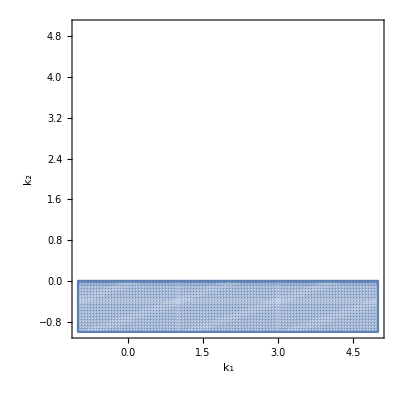

```mathematica
RegionPlot[Exp[k2]<1,{k1,-1,5},{k2,-1,5},PlotPoints->100,FrameLabel->{Subscript[k,1],Subscript[k,2]}]
```

Ahora evaluamos el segundo punto de equilibrio:

```mathematica
MatrixForm[jac1/.{x->k2/k1,y->0}]
```

(1-k2 | ((k1-k2) k2)/k1
0 | k2/k1)

Calculamos sus eigenvalores:

```mathematica
Eigenvalues[{{1-k2,((k1-k2) k2)/k1},{0,k2/k1}}]
```

{1-k2,k2/k1}

Usando la condición en ambos eigenvalores:

```mathematica
TraditionalForm[Abs[λ]<1]
```

Abs[λ]<1

```mathematica
TraditionalForm[Subscript[k,2]/Subscript[k,1]<1]
```

k_2/k_1<1

```mathematica
TraditionalForm[Subscript[k,2]<Subscript[k,1]]
```

k_2<k_1

```mathematica
TraditionalForm[-1<1-Subscript[k,2]<1]
```

-1<1-k_2<1

```mathematica
TraditionalForm[-2<-Subscript[k,2]<0]
```

-2<-k_2<0

```mathematica
TraditionalForm[2>Subscript[k,2]>0]
```

2>k_2>0

Graficando esta región en el espacio de parámetros:

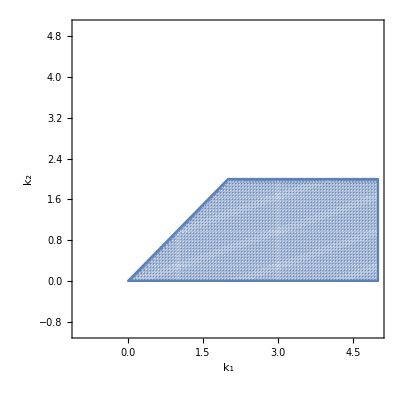

```mathematica
RegionPlot[2>k2>0 && k2<k1,{k1,-1,5},{k2,-1,5},PlotPoints->100,FrameLabel->{Subscript[k,1],Subscript[k,2]}]
```

Finalmente evaluando el útlimo punto de equilibrio

```mathematica
MatrixForm[jac1/.{x->1,y->1}]
```

(1-k1 | k1-k2
1-k1 | 1+k1-k2)

Y calculando sus eigenvalores

```mathematica
Eigenvalues[{{1-k1,k1-k2},{1-k1,1+k1-k2}}]
```

{1/2 (2-k2-√(4 k1-4 k2+k2^2)),1/2 (2-k2+√(4 k1-4 k2+k2^2))}

Los guardamos en variables para determinar donde su módulo es menor a uno después:

```mathematica
eig1=Eigenvalues[{{1-k1,k1-k2},{1-k1,1+k1-k2}}][[1]];
eig2=Eigenvalues[{{1-k1,k1-k2},{1-k1,1+k1-k2}}][[2]];
```

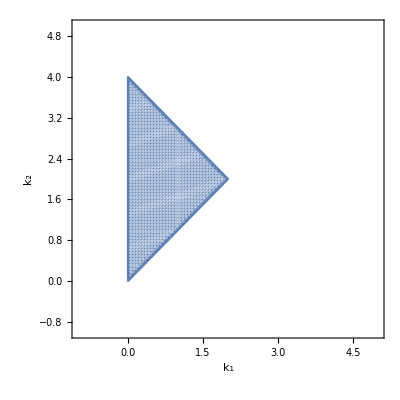

```mathematica
RegionPlot[Abs[eig1]<1 && Abs[eig2]<1,{k1,-1,5},{k2,-1,5},PlotPoints->100,FrameLabel->{Subscript[k,1],Subscript[k,2]}]
```

Gráficamente vemos que la condiciones son :

```mathematica
TraditionalForm[Subscript[k,1]>0]
```

k_1>0

```mathematica
TraditionalForm[Subscript[k,2]>Subscript[k,1]]
```

k_2>k_1

```mathematica
TraditionalForm[Subscript[k,2]<4-Subscript[k,1]]
```

k_2<4-k_1

Poniendo las regiones de estabilidad juntas, obtenemos el diagrama de fases:

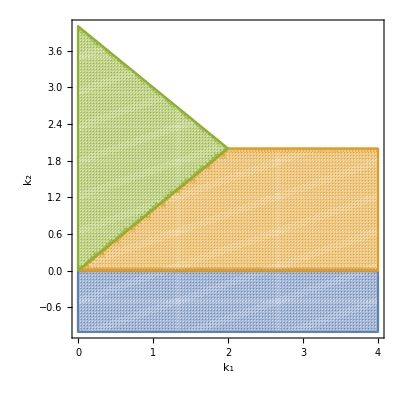

```mathematica
RegionPlot[{Exp[k2]<1,2>k2>0 && k2<k1,Abs[eig1]<1 && Abs[eig2]<1},{k1,0,4},{k2,-1,4},PlotPoints->100,FrameLabel->{Subscript[k,1],Subscript[k,2]}]
```

Ahora podemos estudiar el comportamiento de las soluciones en cada región.
En la región azul:

```mathematica
A=0.9;
α=0.01;
γ=0.02;
b=0.5;
```

```mathematica
sst=RecurrenceTable[{x[k+1]==A*x[k]*Exp[-α*x[k]-γ*y[k]],y[k+1]==A*b*γ*x[k]*y[k]*Exp[-α*x[k]-γ*y[k]],x[1]==10,y[1]==0.001},{x,y},{k,1,200}];
```

Espacio fase:

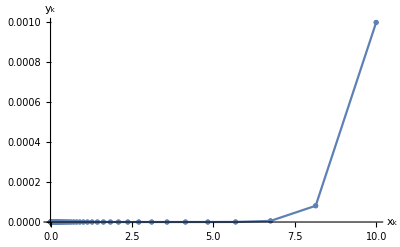

```mathematica
ListPlot[sst,AxesLabel->{Subscript[x,k],Subscript[y,k]},Joined->True,Mesh->Full,PlotRange->All]
```

Soluciones individuales por separado

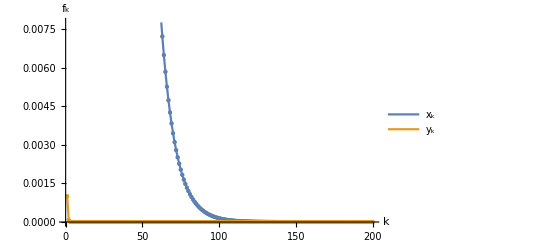

```mathematica
ListPlot[{Table[{k,sst[[k]][[1]]},{k,1,200}],Table[{k,sst[[k]][[2]]},{k,1,200}]},AxesLabel->{k,Subscript[f,k]},Joined->True,Mesh->Full,PlotLegends->{Subscript[x,k],Subscript[y,k]}]
```

En la región verde:

```mathematica
A=10;
α=0.01;
γ=0.02;
b=0.5;
```

```mathematica
sst2=RecurrenceTable[{x[k+1]==A*x[k]*Exp[-α*x[k]-γ*y[k]],y[k+1]==A*b*γ*x[k]*y[k]*Exp[-α*x[k]-γ*y[k]],x[1]==10,y[1]==0.001},{x,y},{k,1,200}];
```

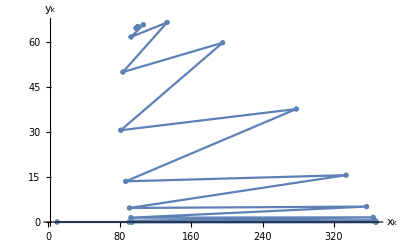

```mathematica
ListPlot[sst2,AxesLabel->{Subscript[x,k],Subscript[y,k]},Joined->True,Mesh->Full,PlotRange->All]
```

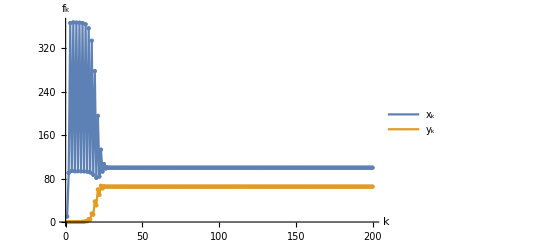

```mathematica
ListPlot[{Table[{k,sst2[[k]][[1]]},{k,1,200}],Table[{k,sst2[[k]][[2]]},{k,1,200}]},AxesLabel->{k,Subscript[f,k]},Joined->True,Mesh->Full,PlotRange->All,PlotLegends->{Subscript[x,k],Subscript[y,k]}]
```

En la región naranja:

```mathematica
A=2;
α=0.01;
γ=0.02;
b=0.5;
```

```mathematica
sst3=RecurrenceTable[{x[k+1]==A*x[k]*Exp[-α*x[k]-γ*y[k]],y[k+1]==A*b*γ*x[k]*y[k]*Exp[-α*x[k]-γ*y[k]],x[1]==10,y[1]==0.001},{x,y},{k,1,200}];
```

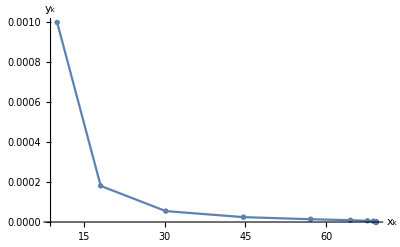

```mathematica
ListPlot[sst3,AxesLabel->{Subscript[x,k],Subscript[y,k]},Joined->True,Mesh->Full,PlotRange->All]
```

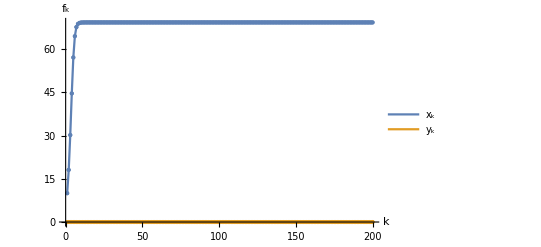

```mathematica
ListPlot[{Table[{k,sst3[[k]][[1]]},{k,1,200}],Table[{k,sst3[[k]][[2]]},{k,1,200}]},AxesLabel->{k,Subscript[f,k]},Joined->True,Mesh->Full,PlotRange->All,PlotLegends->{Subscript[x,k],Subscript[y,k]}]
```

En la región blanca:

```mathematica
A=25;
α=0.01;
γ=0.02;
b=0.5;
```

```mathematica
sst4=RecurrenceTable[{x[k+1]==A*x[k]*Exp[-α*x[k]-γ*y[k]],y[k+1]==A*b*γ*x[k]*y[k]*Exp[-α*x[k]-γ*y[k]],x[1]==10,y[1]==0.001},{x,y},{k,1,200}];
```

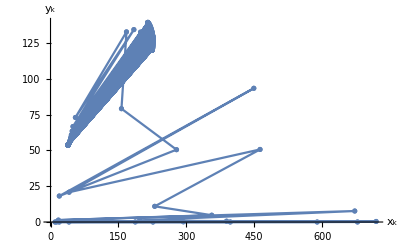

```mathematica
ListPlot[sst4,AxesLabel->{Subscript[x,k],Subscript[y,k]},Joined->True,Mesh->Full,PlotRange->All]
```

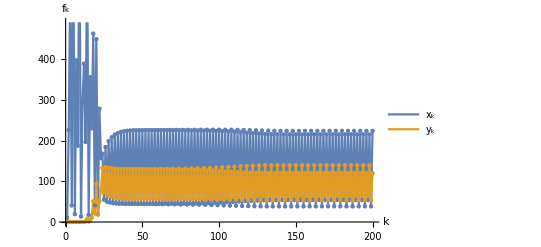

```mathematica
ListPlot[{Table[{k,sst4[[k]][[1]]},{k,1,200}],Table[{k,sst4[[k]][[2]]},{k,1,200}]},AxesLabel->{k,Subscript[f,k]},Joined->True,Mesh->Full,PlotLegends->{Subscript[x,k],Subscript[y,k]}]
```

```mathematica
A=60;
α=0.01;
γ=0.02;
b=0.5;
```

```mathematica
sst5=RecurrenceTable[{x[k+1]==A*x[k]*Exp[-α*x[k]-γ*y[k]],y[k+1]==A*b*γ*x[k]*y[k]*Exp[-α*x[k]-γ*y[k]],x[1]==10,y[1]==0.001},{x,y},{k,1,200}];
```

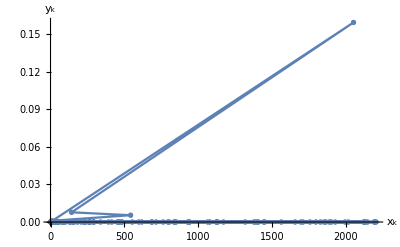

```mathematica
ListPlot[sst5,AxesLabel->{Subscript[x,k],Subscript[y,k]},Joined->True,Mesh->Full,PlotRange->All]
```

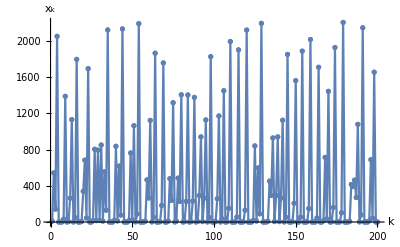

```mathematica
ListPlot[Table[{k,sst5[[k]][[1]]},{k,1,200}],AxesLabel->{k,Subscript[x,k]},Joined->True,Mesh->Full]
```

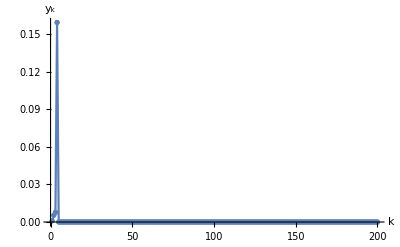

```mathematica
ListPlot[Table[{k,sst5[[k]][[2]]},{k,1,200}],AxesLabel->{k,Subscript[y,k]},Joined->True,Mesh->Full,PlotRange->All]
```